# Programarea Funcțională

## Ininițiere

### Функциональное программирование

Функциональное программирование – ветвь программирования в котором программирование ведется с помощью определения функций и основывается на нескольких важных концепциях:
1. отсутствие побочных эффектов и изменяемых данных,
2. чистые функции и их композиция.

Конечно,  любой программист программирует с помощью функций, да и не только функций, а еще и процедур, циклов, модулей, объектов, ...  Что же отличает функциональное программирование от других парадигм программирования?

В функциональном программировании нет ни процедур, ни циклов, нет даже переменных. Одни функции. Однако, функциональное программирование обладает рядом очень существенных преимуществ.

### Традиционное программирование

Pодилось в 1940 - х годах, когда велась разработка первых компьютеров. Его основой послужила концепция фон Неймана о хранимой программе автоматических вычислений по заданному алгоритму. Существенными чертами такой программы служили:

во - первых, строгая последовательность в выполнении ее элементарных шагов и,

во - вторых, возможность хранения и изменения программы наряду с данными для вычислений в общей с ними памяти.

в третьих, программа сама становилась объектом обработки вместе с арифметическими значениями, над которыми, собственно, и должны были производиться все действия.

Устройство первых компьютеров следовало принципам архитектуры фон Неймана. Исполнение программ сводилось к выполнению арифметическим устройством/процессором элементарных шагов, называемых командами, которые строго последовательно производили определенные действия над арифметическими значениями или другими командами, хранящимися в оперативной памяти компьютера. Изменять команды нужно было для того, чтобы организовать циклическое повторение участков программы и своевременное завершение таких повторений.

### Языки программирования высокого уровня

В конце 1950 - х годов появились первые языки программирования высокого уровня, в них уже произошел существенный отход от принципов фон Неймана.

Во - первых, программа раз и навсегда была отделена от данных.

Во - вторых, во время исполнения программы ее текст оставался неизменным, а организация циклического повторения команд в ходе исполнения программы была возложена на систему программирования, которая уже и должна была перевести (транслировать) текст программы в систему команд компьютера так, чтобы ее исполнение происходило в соответствии с написанным текстом.

Единственный принцип, остававшийся неизменным, был принцип последовательного исполнения, в соответствии с которым исполнение программы можно было разложить на строго последовательные элементарные шаги алгоритма. Поэтому до сих пор программирование в традиционном стиле часто называют «фон - Неймановским» или процедурным.

### Последовательное исполнение комманд и развитие компьютерной техники

Со временем принцип последовательного исполнения стал серьезным препятствием для развития компьютерной техники. Самым узким местом вычислительных систем уже долгое время остается тот самый процессор, который последовательно исполняет элементарные команды. Конечно, скорость работы современных процессоров не сравнить со скоростью работы арифметических устройств первых компьютеров, однако, производительность компьютеров сейчас, как и раньше, ограничена, в основном, именно этим центральным устройством. Именно скорость работы центрального процессора имеет решающее значение при определении общей производительности компьютера.

Скорость работы процессора стала зависеть уже не столько от его архитектуры и технологических элементов, сколько просто от его размеров, потому что на скорость работы решающее влияние стала оказывать скорость прохождения сигналов по цепям процессора, которая, как известно, не может превысить скорости света. Чем меньше процессор, тем быстрее смогут внутри него проходить сигналы, и тем больше оказывается конечная производительность процессора. Размеры процессора уменьшились многократно, однако, все труднее стало отводить от такого миниатюрного устройства вырабатываемое при работе его элементов тепло. Перед производителями вычислительной аппаратуры встал очень серьезный вопрос: дальнейшее повышение производительности стало почти невозможным без изменения основополагающего принципа всего современного программирования – последовательного исполнения команд.

Конечно, можно так спроектировать вычислительную систему, чтобы в ней могли одновременно работать несколько процессоров, но, к сожалению, это почти не дает увеличения производительности, потому что все программы, написанные на традиционных языках программирования, предполагают последовательное выполнение элементарных шагов алгоритма почти так же, как это было во времена фон Неймана. Время от времени предпринимаются попытки ввести в современные языки программирования конструкции для параллельного выполнения фрагментов кода, однако языки “сопротивляются”. Оказывается, думать об организации параллельного выполнения фрагментов программы – это довольно сложная задача, которая успешно решается человеком только для весьма ограниченных случаев.

### Улучшение организации вычислительного процесса

Это можно реализовать различными способами:

Во-первых, можно попробовать написать специальную программу, которая могла бы проанализировать имеющийся программный текст и автоматически выделить в ней фрагменты, которые можно выполнять параллельно. К сожалению, такой анализ произвольного программного кода очень труден. Последовательность выполнения шагов алгоритма очень трудно предсказать по внешнему виду программы, даже если программа «хорошо структурирована».

Второй способ перейти к параллельным вычислениям – это создать такой язык программирования, в котором сам алгоритм имел бы не последовательную структуру, а допускал бы независимое исполнение отдельных частей алгоритма. Но против этого восстает весь накопленный программистами опыт написания программ.

### Функционалные языки

Тем не менее, оказалось, что опыт написания программ, не имеющих строго последовательной структуры, на самом деле есть. Почти одновременно с первым "традиционным" языком программирования – Фортраном, благодаря Джону Маккарти появился еще один совершенно непохожий на него язык программирования – Лисп, для которого последовательность выполнения отдельных частей написанной программы была несущественной.

Ветвь программирования, начатая созданием Лиспа, понемногу развивалась с начала 60-х годов 20 века и привела к появлению целой плеяды очень своеобразных языков программирования, которые удовлетворяли всем требованиям, необходимым для исполнения программ несколькими параллельными процессорами:

Lisp, Python, Scheme, Racket, Erlang, Haskell, Clojure, OCaml, F#.

Во-первых, алгоритмы, записанные с помощью этих языков, допускают сравнительно простой анализ и формальные преобразования программ.

Во-вторых, отдельные части программ могут исполняться независимо друг от друга.

Языки, обладающие такими замечательными свойствами  – это и есть языки функционального программирования.

Помимо своей хорошей приспособленности к параллельным вычислениям языки функционального программирования обладают еще рядом приятных особенностей. Программы на этих языках записываются коротко, часто много короче, чем в любом другом традиционном (императивном) языке. Описание алгоритмов в функциональном стиле сосредоточено не на том, как достичь нужного результата (в какой последовательности выполнять шаги алгоритма), а больше на том, что должен представлять собой этот результат.

Пожалуй, единственный серьезный недостаток функционального стиля программирования состоит в том, что этот стиль не универсальный. Многие действительно последовательные процессы, такие как поведение программных моделей в реальном времени, игровые и другие программы, организующие взаимодействие компьютера с человеком, не выразимы в функциональном стиле. Тем не менее, функциональное программирование заслуживает изучения хотя бы еще и потому, что позволяет несколько по - иному взглянуть вообще на процесс программирования, а некоторые приемы программирования, которые, вообще говоря, предназначены для написания программ в чисто функциональном стиле, могут с успехом использоваться и в традиционном программировании.

```mathematica
{{"Functional Programming", "OOP"},
{"Uses Immutable data","Uses Mutable data"},
{"Follows Declarative Programming Model","Follows Imperative Programming Model"},
{"Focus is on: “What you are doing”","Focus is on “How you are doing”"},
{"Supports Parallel Programming","Not suitable for Parallel Programming"},
{"Its functions have no-side effects","Its methods can produce serious side effects"},
{"Flow Control is done using function calls & function calls with recursion", "Flow control is done using loops and conditional statements"},
{"It uses “Recursion” concept to iterate Collection Data", "It uses “Loop” concept to iterate Collection Data. For example: For-each loop in Java"},
{"Execution order of statements is not so important","Execution order of statements is very important"},
{"Supports both “Abstraction over Data” and “Abstraction over Behavior”", "Supports only “Abstraction over Data”"}}//Grid
```

Functional Programming | OOP
Uses Immutable data | Uses Mutable data
Follows Declarative Programming Model | Follows Imperative Programming Model
Focus is on: “What you are doing” | Focus is on “How you are doing”
Supports Parallel Programming | Not suitable for Parallel Programming
Its functions have no-side effects | Its methods can produce serious side effects
Flow Control is done using function calls & function calls with recursion | Flow control is done using loops and conditional statements
It uses “Recursion” concept to iterate Collection Data | It uses “Loop” concept to iterate Collection Data. For example: For-each loop in Java
Execution order of statements is not so important | Execution order of statements is very important
Supports both “Abstraction over Data” and “Abstraction over Behavior” | Supports only “Abstraction over Data”

Мы будем знакомиться с миром функционального программирования используя один самых передовых языков функционального программирования – Wolfram Language.

# Limbajul Wolfram

## Prezentare generală

## Limbajul Wolfram este un limbaj de programare de nivel înalt, foarte dezvoltat...

## E bazat pe cunoştinţe şi unifică o gamă largă de paradigme de programare.

## Foloseşte conceptul său unic de programare simbolică pentru a adăuga un nou nivel de flexibilitate insăşi conceptului de programare.

Help / Wolfram Documentation / Core Language & Structure / Language Overview

## Expresii simbolice

f[a,b,…] — forma de bază a tuturor lucrurilor în Limbajul Wolfram

```mathematica
b+a+c
```

FullForm[] - functia care ofera forma completă a unei expresii fără utilizarea sintaxei de prescurtare

```mathematica
FullForm[b+a+c]
```

```mathematica
a x^2+π x+ⅇ
```

```mathematica
FullForm[a x^2+π x+ⅇ]
```

Structura expresiilor poate fi cercetată cu ajutorul funcțiilor :

```mathematica
TreeForm[a x^2+π x+ⅇ]
```

```mathematica
Head[a x^2+π x+ⅇ]
```

```mathematica
Length[a x^2+π x+ⅇ]
```

```mathematica
Depth[a x^2+π x+ⅇ]
```

## Liste și Manipularea Expresiilor

```mathematica
{...} (List) ▪...[[...]] (Part) ▪ Table ▪ Length ▪ Take ▪ Select ▪...
```

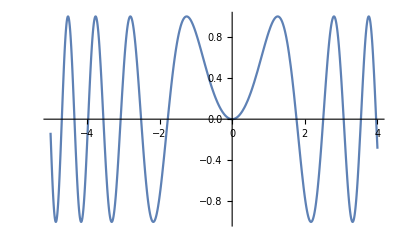
{1,2,3.5,-Graphics-,a,b,-Graphics-,Sir de caractere}

```mathematica
{...}
```